```mathematica
clearVariables[]
setVariables[]

T1 = 5*10^-9;
T2 = 300*10^-9;
Tmax = 2*T1 + T2;

δE = 10^-9;

ΔEMid = 0;
ΔE = 10000 - 12000*twoPointWindow[t, T1, Tmax, 8/12] + δE;
ϵ0Mid = ϵ0 /. ΔE->ΔEMid;

Ea =116.68;
ωE = 2*π*(ϵ0 - A/4 + A*dState[[1]]^2/2) - 2*π*2.0548*10^8 /. ΔE->ΔEMid;

Ba = 0.015131;
ωB = 2*π*(B0*γe - A*dState[[1]]^2/2) - 2*π*1.9759*10^8 /. ΔE->ΔEMid;

UbaseLab = MatrixExp[-ⅈ*t*(HexactStatic /. t->0)];
Ubase0 = MatrixExp[-ⅈ*t*(H0static /. t->0)];
Ubase = MatrixExp[-ⅈ*t*(HcorrectedStatic /. t->0)];

Eamp[t_] := Ea*cosWindow[t - T1, T2/10, T2];
Bamp[t_] := Ba*cosWindow[t - T1, T2/10, T2];

(*Hexactδ = Hexact;
Hcorrectedδ = Hcorrected;*)

statusString="λ = " <> ToString[λ] <> "          ";
U = findEvolutionOperator2D[Hcorrected, Tmax];
(*Ufull = findEvolutionOperator[Hcorrected, Tmax];*)
UU = U /. t->Tmax;

params = gateDecompositionParameters[UU]
```

{3.59827,3.13055,1.74245,0.744053,0.999992}

```mathematica
Clear[toEigenbasis]
toEigenbasis[Uin_, Hin_, tIn_?NumericQ] := (
showStatus["finding eigenbasis at t = " <> ToString[tIn // N // AccountingForm]];
basis0 = statesInOrder[Hin /. t->0];
basisT = statesInOrder[Hin /. t->tIn];
basisT.(Uin /. t->tIn).ConjugateTranspose[basis0]
)
```

```mathematica
T1 = 5*10^-9;
T2 = 300*10^-9;
Tmax = 2*T1 + T2;

ΔE1 = -1300;
ΔE2 = 1300;
δE = 50;

t1 = (T2/4000)(ΔE1 + 2000) + T1;
t2 = (T2/4000)(ΔE2 + 2000) + T1;

t1δ = (T2/4000)(ΔE1 + 2000 - δE) + T1;
t2δ = (T2/4000)(ΔE2 + 2000 - δE) + T1;

(*Ubase.ConjugateTranspose[UbaseLab].Ufull/. t->150*10^-9 // MatrixForm;
toEigenbasis[Ubase.ConjugateTranspose[UbaseLab].Ufull, Hcorrected, 150*10^-9] // MatrixForm;*)

(*(Ufull /. t->t2).ConjugateTranspose[(Ufull /. t->t1)] // MatrixForm
(Ufullδ /. t->t2δ).ConjugateTranspose[(Ufullδ /. t->t1δ)] // MatrixForm*)

(*toEigenbasis[Ufull, Hcorrected, t1] // MatrixForm*)

Print["--------------------NO NOISE-----------------------"]
(* paramreters of pieces without noise *)
Ustart = toEigenbasis[Ufull, Hcorrected, t1];
Ustart[[{1, 2}, {1, 2}]] // MatrixForm

Umid = toEigenbasis[Ufull, Hcorrected, t2].ConjugateTranspose[toEigenbasis[Ufull, Hcorrected, t1]];
Umid[[{1, 2}, {1, 2}]] // MatrixForm

Uend = toEigenbasis[Ufull, Hcorrected, Tmax].ConjugateTranspose[toEigenbasis[Ufull, Hcorrected, t2]];
Uend[[{1, 2}, {1, 2}]] // MatrixForm

gateDecompositionParameters[Ustart[[{1, 2}, {1, 2}]]]
-(%[[1]] + %[[3]])
gateDecompositionParameters[Umid[[{1, 2}, {1, 2}]]]
%[[1]] - %[[3]]
gateDecompositionParameters[Uend[[{1, 2}, {1, 2}]]]
%[[1]] + %[[3]]
gateDecompositionParameters[Ufull[[{1, 2}, {1, 2}]] /. t->Tmax]
%[[1]] - %[[3]]

Print["--------------------NOISE-----------------------"]
(* paramreters of pieces with noise *)
Ustart = toEigenbasis[Ufullδ, Hcorrected, t1δ];
Ustart[[{1, 2}, {1, 2}]] // MatrixForm

Umid = toEigenbasis[Ufullδ, Hcorrected, t2δ].ConjugateTranspose[toEigenbasis[Ufullδ, Hcorrected, t1δ]];
Umid[[{1, 2}, {1, 2}]] // MatrixForm

Uend = toEigenbasis[Ufullδ, Hcorrected, Tmax].ConjugateTranspose[toEigenbasis[Ufullδ, Hcorrected, t2δ]];
Uend[[{1, 2}, {1, 2}]] // MatrixForm

gateDecompositionParameters[Ustart[[{1, 2}, {1, 2}]]]
-(%[[1]] + %[[3]])
gateDecompositionParameters[Umid[[{1, 2}, {1, 2}]]]
%[[1]] - %[[3]]
gateDecompositionParameters[Uend[[{1, 2}, {1, 2}]]]
%[[1]] + %[[3]]
gateDecompositionParameters[Ufullδ[[{1, 2}, {1, 2}]] /. t->Tmax]
%[[1]] - %[[3]]



(*Ufull /. t->Tmax // MatrixForm
Ufullδ /. t->Tmax // MatrixForm
ConjugateTranspose[Ufull /. t->Tmax].(Ufullδ /. t->Tmax) // MatrixForm*)
```

--------------------NO NOISE-----------------------

(0.737924-0.674755 ⅈ | -0.0120255-0.00416832 ⅈ
0.00336152+0.0122753 ⅈ | -0.722218+0.691547 ⅈ)

(0.00194117-0.000660047 ⅈ | 0.9684+0.249394 ⅈ
-0.723347-0.690482 ⅈ | 0.000465077+0.00199687 ⅈ)

(-0.817952-0.575178 ⅈ | -0.000239304-0.0111044 ⅈ
-0.0101002-0.00462072 ⅈ | 0.203895+0.978928 ⅈ)

{5.80976,0.0254557,3.63801,0.818586,0.999993}

-9.44777

{3.62247,3.13749,0.990981,0.507106,1.}

2.63149

{1.7546,0.0222145,0.634412,5.70155,0.999998}

2.38901

{3.59827,3.13055,1.74245,0.744053,0.999992}

1.85582

--------------------NOISE-----------------------

(-0.43069-0.902323 ⅈ | -0.00363748+0.016816 ⅈ
0.0171911+0.000708782 ⅈ | 0.765003+0.643789 ⅈ)

(0.00266345-0.00214876 ⅈ | 0.968379+0.249408 ⅈ
-0.723347-0.690455 ⅈ | -0.000420409+0.00339816 ⅈ)

(0.113563-0.993507 ⅈ | 0.00550277-0.0016671 ⅈ
-0.00371976-0.00438518 ⅈ | -0.4431+0.896446 ⅈ)

{5.79665,0.0344119,4.05403,5.6249,0.999983}

-9.85067

{3.2714,3.13475,0.639875,0.507105,0.999972}

2.63153

{2.38836,0.0114997,0.407979,0.286439,0.999986}

2.79634

{2.9637,3.12429,1.10336,0.135264,0.999992}

1.86033

```mathematica
Mod[-4.4859755350465225 + 5.298216447485197 + 7.326543336337859, 2π]
```

1.8556

```mathematica
Hcorrected /. t->t1 // MatrixForm
Hcorrectedδ /. t->t1δ // MatrixForm
```

(-1.07636×10^7 | 0. | 6.6478×10^8 | 0 | -5.59651×10^8 | -1685.62 | 0 | 0
0. | -1.62705×10^8 | -1.12448×10^6 | 6.64786×10^8 | 0 | -5.56674×10^8 | 0 | 0
6.6478×10^8 | -1.12448×10^6 | 1.09173×10^9 | 0. | 0 | -1.53973×10^8 | -5.56106×10^8 | 1693.38
0 | 6.64786×10^8 | 0. | 1.50742×10^9 | 0 | 0 | 0 | -5.59081×10^8
-5.59651×10^8 | 0 | 0 | 0 | 7.90779×10^9 | 0. | 6.64782×10^8 | 0
-1685.62 | -5.56674×10^8 | -1.53973×10^8 | 0 | 0. | 7.95785×10^9 | 1.12477×10^6 | 6.64784×10^8
0 | 0 | -5.56106×10^8 | 0 | 6.64782×10^8 | 1.12477×10^6 | 9.24654×10^9 | 0.
0 | 0 | 1693.38 | -5.59081×10^8 | 0 | 6.64784×10^8 | 0. | 9.46397×10^9)

(-1.07636×10^7 | 0. | 6.6478×10^8 | 0 | -5.59651×10^8 | -1685.62 | 0 | 0
0. | -1.62705×10^8 | -1.12448×10^6 | 6.64786×10^8 | 0 | -5.56674×10^8 | 0 | 0
6.6478×10^8 | -1.12448×10^6 | 1.09173×10^9 | 0. | 0 | -1.53973×10^8 | -5.56106×10^8 | 1693.38
0 | 6.64786×10^8 | 0. | 1.50742×10^9 | 0 | 0 | 0 | -5.59081×10^8
-5.59651×10^8 | 0 | 0 | 0 | 7.90779×10^9 | 0. | 6.64782×10^8 | 0
-1685.62 | -5.56674×10^8 | -1.53973×10^8 | 0 | 0. | 7.95785×10^9 | 1.12477×10^6 | 6.64784×10^8
0 | 0 | -5.56106×10^8 | 0 | 6.64782×10^8 | 1.12477×10^6 | 9.24654×10^9 | 0.
0 | 0 | 1693.38 | -5.59081×10^8 | 0 | 6.64784×10^8 | 0. | 9.46397×10^9)

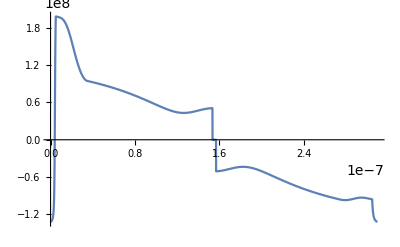

```mathematica
Plot[energiesInOrder[Hcorrected /. t->tt][[1]] - energiesInOrder[Hcorrected /. t->tt][[2]], {tt, 0, Tmax}]
```

```mathematica
eIOintegrable[M_, tt_?NumericQ]:=energiesInOrder[M]
NIntegrate[eIOintegrable[Hcorrected /. t->tt, tt][[1]], {tt, T1, t1}]

(*NIntegrate[eIOintegrable[Hcorrected /. t->tt, tt][[1]] - eIOintegrable[Hcorrected /. t->tt, tt][[2]], {tt, T1, t1}]
NIntegrate[eIOintegrable[Hcorrected /. t->tt, tt][[1]] - eIOintegrable[Hcorrected /. t->tt, tt][[2]], {tt, t2, T1 + T2}]*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{{-0.314469,0.,24.9292,0.,-17.6358,-0.0000493343,0.,0.},{0.,-10.079,-0.027046,24.9295,0.,-17.5228,0.,0.},{24.9292,-0.027046,55.258,0.,0.,-6.59096,-17.5012,0.0000495723},{0.,24.9295,0.,78.8099,0.,0.,0.,-17.6142},{-17.6358,0.,0.,0.,920.994,0.,24.9293,0.},{-0.0000493343,-17.5228,-6.59096,0.,0.,925.391,0.0270541,24.9294},{0.,0.,-17.5012,0.,24.9293,0.0270541,993.121,0.},{0.,0.,0.0000495723,-17.6142,0.,24.9294,0.,1002.79}}

```mathematica
energiesInOrder[Hcorrected /. t->t1][[1]] - energiesInOrder[Hcorrected /. t->t1][[2]]
energiesInOrder[Hcorrected /. t->t2][[1]] - energiesInOrder[Hcorrected /. t->t2][[2]]
```

8.44475×10^7

-8.60077×10^7

```mathematica
Hcorrected /. t->t1 // MatrixForm
```

(-9.8458×10^6 | 0. | 6.6478×10^8 | 0 | -5.10255×10^8 | -1475.36 | 0 | 0
0. | -1.80518×10^8 | -886454. | 6.64787×10^8 | 0 | -5.07168×10^8 | 0 | 0
6.6478×10^8 | -886454. | 1.07097×10^9 | 0. | 0 | -1.40266×10^8 | -5.06579×10^8 | 1482.28
0 | 6.64787×10^8 | 0. | 1.50478×10^9 | 0 | 0 | 0 | -5.09663×10^8
-5.10255×10^8 | 0 | 0 | 0 | 1.1962×10^10 | 0. | 6.64782×10^8 | 0
-1475.36 | -5.07168×10^8 | -1.40266×10^8 | 0 | 0. | 1.20306×10^10 | 886706. | 6.64784×10^8
0 | 0 | -5.06579×10^8 | 0 | 6.64782×10^8 | 886706. | 1.33225×10^10 | 0.
0 | 0 | 1482.28 | -5.09663×10^8 | 0 | 6.64784×10^8 | 0. | 1.35217×10^10)